## Automated process for creating graphical representation with the Wigner-D functions

```mathematica
ClearAll["Global`*"]
```

### Author: Robert Poenaru Date: 25th August 🗓

### Constant spin for a system

```mathematica
spin=3;
theta=π/3;
phi=π/6;
psi=π/2;
```

Create a set of projections M and K,  for a given spin I

```mathematica
wfComp[spin_]:=Table[{spin,m,k},{m,-spin,spin},{k,-spin,spin}];
```

Generate a set of Euler Angles using a pure function

```mathematica
angles[]={RandomReal[{π/6,π}],RandomReal[{π/6,π}],RandomReal[{π/6,π}]};
```

Create the first state φ_0=|I M=-I K=-I>

```mathematica
state0=wfComp[spin][[1]];
```

```mathematica
printer[state_]:=Do[Print["|IMK> = ","|",state[[i,1]]," ",state[[i,2]]," ",state[[i,3]]," >"],{i,1,2*spin+1}];
printer[state0]
```

|IMK> = |3 -3 -3 >

|IMK> = |3 -3 -2 >

|IMK> = |3 -3 -1 >

|IMK> = |3 -3 0 >

|IMK> = |3 -3 1 >

|IMK> = |3 -3 2 >

|IMK> = |3 -3 3 >

```mathematica
wigner[state_]:=Table[WignerD[state[[i]],angles[][[1]],angles[][[2]],angles[][[3]]],{i,1,2*spin+1}];
(*Create the real Wigner-D functions*)
rwd[state_]:=Table[Re[wigner[state][[i]]],{i,1,Length[wigner[state]]}];
```

Create plotting functions for Wigner-𝒟 functions

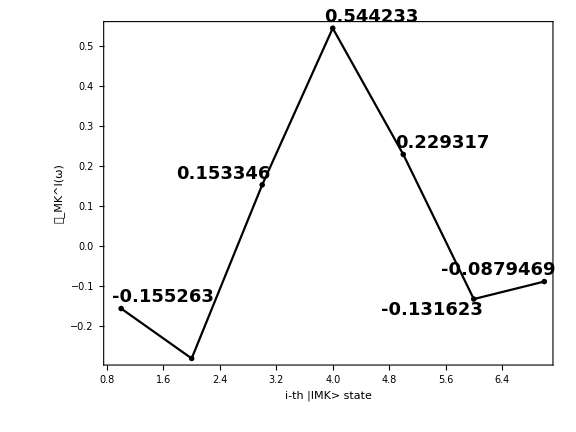

```mathematica
plotWD[state_]:=ListPlot[Labeled[#,#]&/@Table[rwd[state][[i]],{i,1,Length[wigner[state]]}],PlotRange->Full,Axes->False,Frame->True,PlotStyle->Black,PlotMarkers->{Blue,Large},Joined->True,FrameLabel->{"i-th |IMK> state","𝒟_MK^I(ω)"},LabelStyle->{18,Bold,Black,FontFamily->"Times"},ImageSize->Large,FrameStyle->Directive[Black,Thick],PlotRange->Full,AspectRatio->0.75];
Show[plotWD[state0]]
```